# Population History Analysis :: HMSC

## Functions

```mathematica
SwitchNote[test_]:=Switch[test,
"D","C4",
"M","D4",
"F","E4",
"B","F4",
"R","G4",
"L","A4",
"O","B4",
"S","C5",
"E","D5"
]
SoundDissectMosquito[mosquitoEvents_,voice_]:=Module[{intervals,notes,times,timesFinal},
intervals=GetMosquitoIntervals[mosquitoEvents];
notes=SwitchNote/@intervals[[All,1]];
times={#[[1,1]],#[[1,2]]}&/@intervals[[All,2]];
timesFinal=ReplacePart[times-times[[1,1]],{Length[times],2}->times[[Length[times],1]]-times[[1,1]]+2];
(Apply[SoundNote,Append[#,voice]]&/@Transpose[{notes,timesFinal}])//Sound
]
GetMosquitoStatesAtTimeStamp[intervals_,tick_]:=Flatten[Cases[#,{a_,b_}/;IntervalMemberQ[b,tick]->a]&/@intervals]
TallyElements[filteredRange_]:={
{"D",Count[filteredRange,"D"]},
{"F",Count[filteredRange,"F"]},
{"S",Count[filteredRange,"S"]},
{"L",Count[filteredRange,"L"]},
{"O",Count[filteredRange,"O"]},
{"B",Count[filteredRange,"B"]},
{"R",Count[filteredRange,"R"]},
{"M",Count[filteredRange,"M"]},
{"E",Count[filteredRange,"E"]}
}
FilterByTime[events_,{minT_,maxT_}]:=Cases[events,(a_->b_)/;(a≥minT&&a<maxT)->b]
GenerateRanges[{min_,max_,step_}]:=Partition[Range[min,max,step],2,1]
TallyFilteredRange[events_,{minT_,maxT_,step_}]:=Module[{range,filteredRange,tally},
range=GenerateRanges[{minT,maxT,step}];
filteredRange=TallyElements[FilterByTime[events,#]]&/@range
]
TallyFilteredRangeTrueCount[events_,{minT_,maxT_,step_}]:=Module[{ranges,filtered,range,filteredRange,tally},
ranges=GenerateRanges[{minT,maxT,step}];
filtered=FilterMosquitosEventsInRange[events,#]&/@ranges;
TallyElements[#]&/@filtered;
]
FilterMosquitosEventsInRange[eventTimes_,{min_,max_}]:=Module[{filtered},
filtered=FilterByTime[#,{min,max}]&/@eventTimes;
(If[Length[#]>0,#//Last,##&[]])&/@filtered
]

PlotMosquitoIntervals[mosquito_,id_]:=Module[{intervals,binned,key},
Clear[b];
intervals=GetMosquitoIntervals[mosquito];
key={"D","M","F","B","R","L","O","S","E","X"};
binned=Cases[intervals,{#,b_}->b]&/@key;
NumberLinePlot[binned
,PlotLegends->None
,Frame->True
,FrameStyle->Thick
,BaseStyle->Directive[Thick,25]
,GridLines->{None,{#,Thickness[.001]}&/@Range[key//Length]}
,PlotStyle->Directive[{"Pastel",Thickness[.01]}]
,ImageSize->800
,FrameTicks->{
{Transpose[{Range[(key//Length)-1],key[[1;;Length[key]-1]]}],Automatic},
{Automatic,None}
}
,PlotLabel->("Dissecting: "<>id)
,PlotRange->{{Min[mosquito[[All,1]]]-1,Max[mosquito[[All,1]]]+1},{0,Length[key]-1}}
]
]
```

```mathematica
(*
[[All,1]]: ID,
[[All,2]]: States,
[[All,2,1]]: stateH,
[[All,2,2]]: ixH,
[[All,2,3]]: feedAllH,
[[All,2,4]]: pSetH,
[[All,2,5]]: timeH,
[[All,2,6]]: batchH,
[[All,2,7]]: feedAllT,
[[All,2,8]]: feedHumanH,
[[All,2,9]]: bmSizeH,
[[All,2,10]]: feedIxH,
[[All,2,11]]: feedHumanT
*)
```

## Males

## Import Data Males

```mathematica
GetMosquitoTimeEvents[mosquito_]:=Module[{states,times},
states=Cases[mosquito,Rule["stateH",a_]->a];
times=Cases[mosquito,Rule["timeH",a_]->a];
(#[[1]]->#[[2]])&/@(Transpose[{times,states}])
]
```

```mathematica
SetDirectory[NotebookDirectory[]<>"/Debug/MOSQUITO/"]
fileNames=FileNames["*.json"];
kind="Male";
bools=Select[fileNames,StringMatchQ[#,kind<>"MosquitoHistory"~~___]&];
femalesRaw=(Import/@bools)[[1]];
eventTimes=GetMosquitoTimeEvents/@femalesRaw;
sortedEvents=Flatten[eventTimes]//Sort;
```

/Users/sanchez.hmsc/Documents/GitHub/MASH-Main/MASH-dev/HectorSanchez/VectorControl/Debug/MOSQUITO

## Dissect Mosquito

```mathematica
mosquito=femalesRaw[[1]]
mosquito[[3,2]]

states=mosquito[[All,2]][[2;;Length[mosquito[[All,2]]]-1]]
intervals=Partition[mosquito[[All,2]],2,1]
```

{ID→{0_10_1},stateH→{emerge,M,D},pSetH→{l,m},timeH→{0,0,1.2619},ixH→{1,10}}

{l,m}

{{emerge,M,D},{l,m},{0,0,1.2619}}

{{{0_10_1},{emerge,M,D}},{{emerge,M,D},{l,m}},{{l,m},{0,0,1.2619}},{{0,0,1.2619},{1,10}}}

```mathematica
transposed=Append[Transpose[{states,intervals}],{"D",Interval[{Last[mosquito][[1]],∞}]}]
```

```mathematica
GetMosquitoIntervals[mosquito_]:=Module[{states,intervals,transposed},
states=mosquito[[All,2]][[1;;Length[mosquito[[All,2]]]-1]];
intervals=Interval/@Partition[mosquito[[All,1]],2,1];
transposed=Append[Transpose[{states,intervals}],{"D",Interval[{Last[mosquito][[1]],∞}]}]
]
GetMosquitoIntervals[femalesRaw[[1]]]
```

{{{0_10_1},Interval[{ID,stateH}]},{{emerge,M,D},Interval[{stateH,pSetH}]},{{l,m},Interval[{pSetH,timeH}]},{{0,0,1.2619},Interval[{timeH,ixH}]},{D,Interval[{ixH,∞}]}}

StringJoin::string: String expected at position 2 in Dissecting: <>(ID→{0_10_1})<>(stateH→{emerge,M,D})<>(pSetH→{l,m})<>(timeH→{0,0,1.2619})<>(ixH→{1,10}).

StringJoin::string: String expected at position 3 in Dissecting: <>(ID→{0_10_1})<>(stateH→{emerge,M,D})<>(pSetH→{l,m})<>(timeH→{0,0,1.2619})<>(ixH→{1,10}).

StringJoin::string: String expected at position 4 in Dissecting: <>(ID→{0_10_1})<>(stateH→{emerge,M,D})<>(pSetH→{l,m})<>(timeH→{0,0,1.2619})<>(ixH→{1,10}).

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

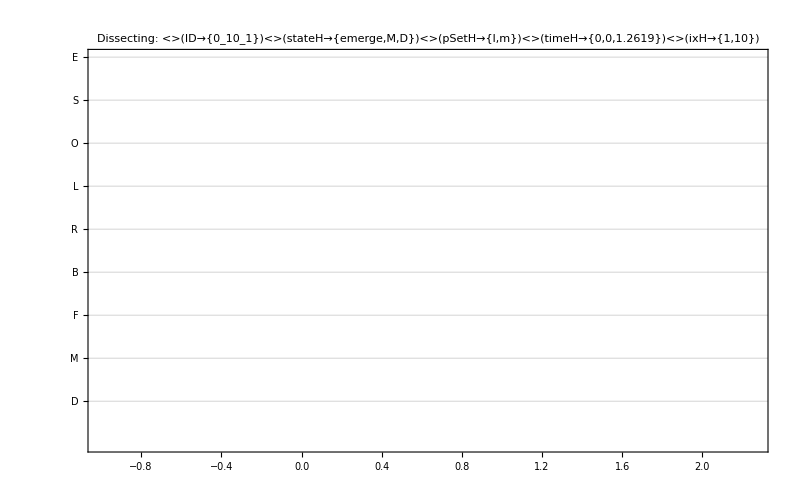

```mathematica
index=1;
mosquitoId=femalesRaw[[index]];
mosquitoEvents=eventTimes[[index]];
PlotMosquitoIntervals[mosquitoEvents,mosquitoId]
```

```mathematica
Table[
index=i;
mosquitoId=femalesRaw[[index]][[1]];
mosquitoEvents=eventTimes[[index]];
Export[kind<>"_"<>mosquitoId<>".png",PlotMosquitoIntervals[mosquitoEvents,mosquitoId]]
,{i,RandomInteger[{1,femalesRaw//Length},20]}]
```

StringJoin::string: String expected at position 2 in Male_<>(ID→{0_10_1})<>(stateH→{emerge,M,D})<>(pSetH→{l,m})<>(timeH→{0,0,1.2619})<>(ixH→{1,10})<>.png.

StringJoin::string: String expected at position 3 in Male_<>(ID→{0_10_1})<>(stateH→{emerge,M,D})<>(pSetH→{l,m})<>(timeH→{0,0,1.2619})<>(ixH→{1,10})<>.png.

StringJoin::string: String expected at position 4 in Male_<>(ID→{0_10_1})<>(stateH→{emerge,M,D})<>(pSetH→{l,m})<>(timeH→{0,0,1.2619})<>(ixH→{1,10})<>.png.

General::stop: Further output of StringJoin::string will be suppressed during this calculation.

Export::chtype: First argument Male_<>(ID→{0_10_1})<>(stateH→{emerge,M,D})<>(pSetH→{l,m})<>(timeH→{0,0,1.2619})<>(ixH→{1,10})<>.png is not a valid file specification.

General::stop: Further output of Export::chtype will be suppressed during this calculation.

{$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed,$Failed}

## Population Counts

```mathematica
intervals=ParallelMap[GetMosquitoIntervals[#]&,eventTimes];
timeRange=Range[1,120,1];
(**)
mosquitoStatesAtTicks=ParallelMap[GetMosquitoStatesAtTimeStamp[intervals,#]&,timeRange];
tallies=ParallelMap[TallyElements[#]&,mosquitoStatesAtTicks];
talliesWithoutDead=Cases[#,{a_,_}/;a≠"D"]&/@tallies;
```

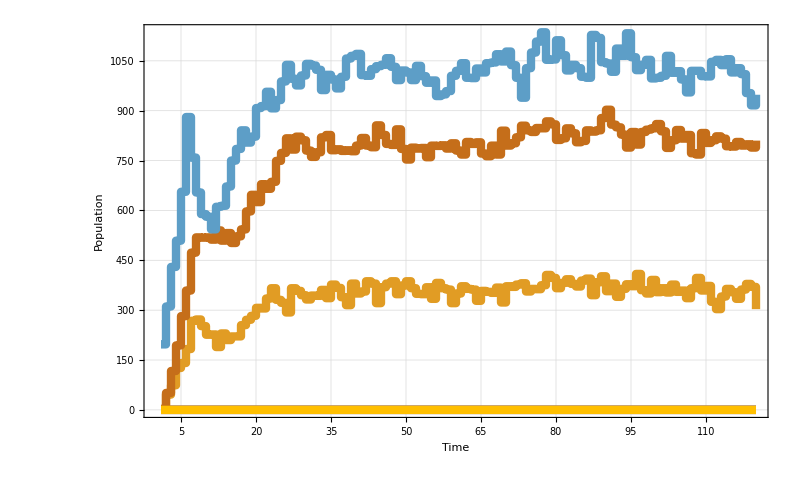
-Graphics- |

M_plot.png

```mathematica
plot=ListLinePlot[
Transpose[#[[All,2]]&/@talliesWithoutDead]
,PlotLegends->None
,Frame->True
,FrameStyle->Thick
,BaseStyle->Directive[Thick,15]
,PlotRange->All
,GridLines->Automatic
,PlotStyle->Directive[{Opacity[1],Thickness[.0075]}]
,ImageSize->800
,FrameLabel->(Style[#,30]&/@{"Time","Population"})
,FrameTicks->{
{Automatic,Automatic},
{Last/@Partition[Transpose[{Range[Length[timeRange]],timeRange}],5],None}
}
,InterpolationOrder->0
];
colors=Cases[plot,{___,c_Directive,__Line}:>ColorConvert[c,RGBColor],Infinity];
swatch=SwatchLegend[
colors,
talliesWithoutDead[[5,All,1]]
,LegendMarkerSize->25
,LabelStyle->25
];
Grid[{{plot,swatch}}]
Export[kind<>"_"<>"plot.png",%,ImageSize->1000]
```

## Females

## Import Data Females

```mathematica
SetDirectory[ParentDirectory[NotebookDirectory[]]<>"/OUTPUT/"]
fileNames=FileNames["*.json"];
kind="F";
bools=Select[fileNames,StringMatchQ[#,"history"<>kind~~___]&];
femalesRaw=Flatten[Import/@bools];
eventTimes=GetMosquitoTimeEvents/@femalesRaw;
sortedEvents=Flatten[eventTimes]//Sort;
```

/Users/chipdelmal/Documents/School/Research/MASH/MAIN/OUTPUT

## Dissect Mosquito

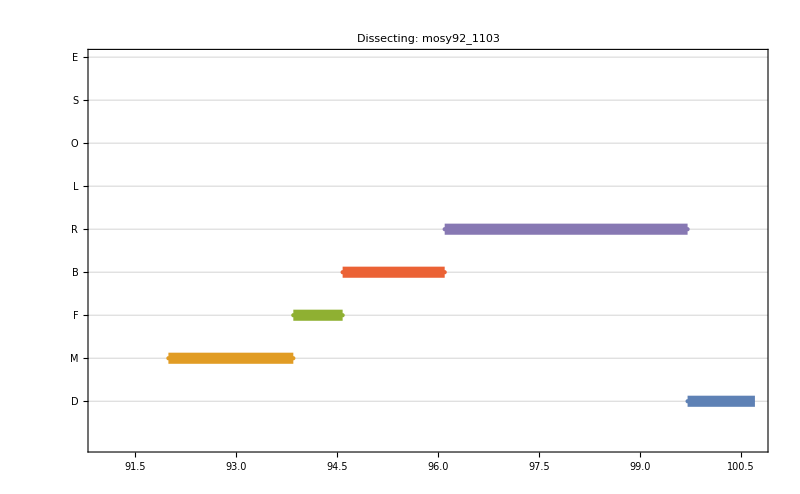

probed.png

```mathematica
index=120;
mosquitoId=femalesRaw[[index]][[1]];
mosquitoEvents=eventTimes[[index]];
PlotMosquitoIntervals[mosquitoEvents,mosquitoId]
Export["probed.png",%]
```

```mathematica
Table[
index=i;
mosquitoId=femalesRaw[[index]][[1]];
mosquitoEvents=eventTimes[[index]];
Export[kind<>"_"<>mosquitoId<>".png",PlotMosquitoIntervals[mosquitoEvents,mosquitoId]]
,{i,RandomInteger[{1,femalesRaw//Length},20]}]
```

{F_mosy1_234.png,F_mosy23_2127.png,F_mosy96_3837.png,F_mosy59_7650.png,F_mosy19_7289.png,F_mosy118_6492.png,F_mosy65_2770.png,F_mosy1_365.png,F_mosy61_563.png,F_mosy71_152.png,F_mosy119_7577.png,F_mosy96_3806.png,F_mosy47_5425.png,F_mosy18_6689.png,F_mosy70_6432.png,F_mosy98_5778.png,F_mosy76_3575.png,F_mosy18_6617.png,F_mosy111_371.png,F_mosy78_6858.png}

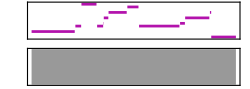

probed.mp3

```mathematica
sound=SoundDissectMosquito[mosquitoEvents,"Violin"]
Export["probed.mp3",%]
```

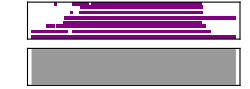

symphony.mp3

```mathematica
symphony=Flatten[eventTimes[[1;;2000]]];
SoundDissectMosquito[symphony,"Piano"]
Export["symphony.mp3",%]
```

## Population Counts

```mathematica
intervals=ParallelMap[GetMosquitoIntervals[#]&,eventTimes];
timeRange=Range[1,125,1];
(**)
mosquitoStatesAtTicks=ParallelMap[GetMosquitoStatesAtTimeStamp[intervals,#]&,timeRange];
tallies=ParallelMap[TallyElements[#]&,mosquitoStatesAtTicks];
talliesWithoutDead=Cases[#,{a_,_}/;a≠"D"]&/@tallies;
```

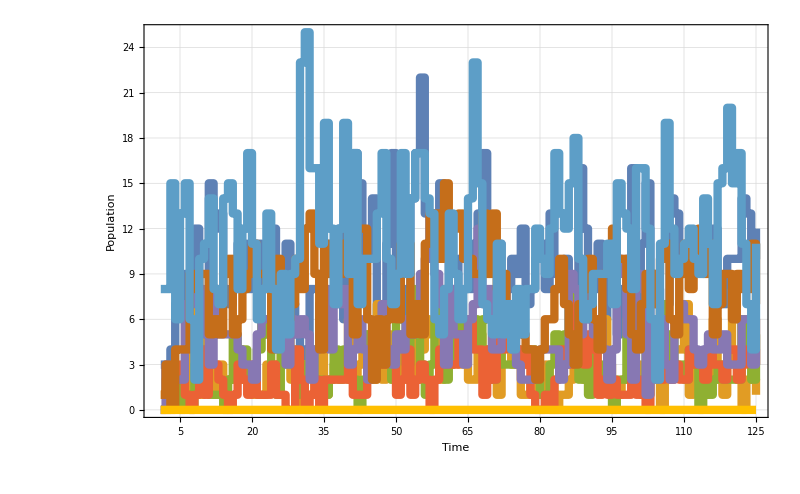
-Graphics- |

F_plot.png

```mathematica
plot=ListLinePlot[
Transpose[#[[All,2]]&/@talliesWithoutDead]
,PlotLegends->None
,Frame->True
,FrameStyle->Thick
,BaseStyle->Directive[Thick,15]
,PlotRange->All
,GridLines->Automatic
,PlotStyle->Directive[{Opacity[1],Thickness[.0075]}]
,ImageSize->800
,FrameLabel->(Style[#,30]&/@{"Time","Population"})
,FrameTicks->{
{Automatic,Automatic},
{Last/@Partition[Transpose[{Range[Length[timeRange]],timeRange}],5],None}
}
,InterpolationOrder->0
];
colors=Cases[plot,{___,c_Directive,__Line}:>ColorConvert[c,RGBColor],Infinity];
swatch=SwatchLegend[
colors,
talliesWithoutDead[[5,All,1]]
,LegendMarkerSize->25
,LabelStyle->25
];
Grid[{{plot,swatch}}]
Export[kind<>"_"<>"plot.png",%,ImageSize->1000]
```